```mathematica
Quit[]
```

```mathematica
2
```

2

```mathematica
CreatePacletArchive["/Users/andrewyule/Dropbox (Personal)/AFS/Source Code/ggplot/ggplot","Downloads"]
PacletInstall[%,ForceVersionInstall->True]
```

/Users/andrewyule/Downloads/ggplot-0.1.paclet

PacletObject[…]

```mathematica
Get["Alex`"]
Get["ggplot`"]
```

Assured Flow Solutions' Alex v2020.4.13

ggplot v0.1

Get data sets

```mathematica
mpg=FileNameJoin[{NotebookDirectory[],"Data","mpg.csv"}]//importToDataset;
```

```mathematica
mtcars=FileNameJoin[{NotebookDirectory[],"Data","mtcars.csv"}]//importToDataset;
```

```mathematica
(*diamonds=FileNameJoin[{NotebookDirectory[],"Data","diamonds.csv"}]//importToDataset;*)
```

#### Faster ability to put Points in a Graphics object

GeometricTransformation can be used to take a single Inset command and replicate it at multiple locations

```mathematica
Graphics[{Red,Point[{{0,0},{1,1}}],
Blue,GeometricTransformation[Inset["A",{0,0}],{{{0.5,0.5}},{{1,1}}}]
}]
```

-Graphics-

```mathematica
GeometricTransformation[Inset[Style[■,Rule[GraphicsBoxOptions,List[Rule[DefaultBaseStyle,Directive[PointSize[0.012833333333333334],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]]]]]],List[0.,0.]],List[List[List[0.,0.]],List[List[1.,1.]]]]//InputForm
```

GeometricTransformation[
 Inset[Style[■, GraphicsBoxOptions -> 
    {DefaultBaseStyle -> Directive[PointSize[0.012833333333333334], 
       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]]}], {0., 0.}], 
 {{{0., 0.}}, {{1., 1.}}}]

```mathematica
GeometricTransformation
```

```mathematica
ListPlot[{{0,0},{1,1}},PlotMarkers->■]//FullForm
```

Graphics[List[List[],List[List[List[Directive[PointSize[0.0128333],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],GeometricTransformation[Inset[Style[\[FilledSquare],Rule[GraphicsBoxOptions,List[Rule[DefaultBaseStyle,Directive[PointSize[0.0128333],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]]]]]],List[0.,0.]],List[List[List[0.,0.]],List[List[1.,1.]]]]]],List[List[Directive[PointSize[0.0128333],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]]],List[]],List[List[Directive[PointSize[0.0128333],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]]],List[]]],List[List[],List[]]],List[Rule[DisplayFunction,Identity],Rule[DisplayFunction,Identity],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[Method,List[Rule["OptimizePlotMarkers",True],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[0,1.],List[0,1.]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.02],Scaled[0.05]]]],Rule[Ticks,List[Automatic,Automatic]]]]

#### Experimenting

```mathematica
mtcars[[1]]
```

<|mpg→21,cyl→6,disp→160,hp→110,drat→3.9,wt→2.62,qsec→16.46,vs→0,am→1,gear→4,carb→4|>

```mathematica
geomParityLine[mtcars]
geomHLine[mtcars,"y"->10]
geomVLine[mtcars,"x"->10]
```

{{GrayLevel[0],Opacity[1],Thickness[Large],InfiniteLine[{{0,0},{1,1}}]}}

{{GrayLevel[0],Opacity[1],Thickness[Large],InfiniteLine[{{0,10},{1,10}}]}}

{{GrayLevel[0],Opacity[1],Thickness[Large],InfiniteLine[{{10,0},{10,1}}]}}

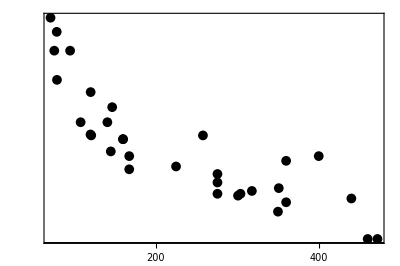

```mathematica
ggplot[mtcars,{geomPoint["x"->"disp","y"->"mpg"],geomParityLine[],geomHLine["y"->10],geomVLine["x"->10]}]
```

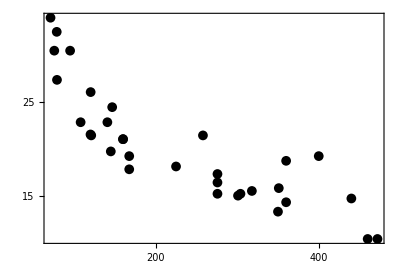

```mathematica
ggplot[mtcars,geomPoint["x"->"disp","y"->"mpg"]]
(*mtcars//ggplot[geomPoint["x"->"disp","y"->"mpg"]]*)
```

```mathematica
geomPoint[mtcars,"y"->"disp","x"->"mpg","color"->"cyl"]
```

{{RGBColor[Rational[1, 2], 0, Rational[1, 2]],Opacity[1],GeometricTransformation[Inset[●,{0,0}],{{{21,160}},{{21,160}},{{21.4,258}},{{18.1,225}},{{19.2,167.6}},{{17.8,167.6}},{{19.7,145}}}]},{RGBColor[1, 0, 0],Opacity[1],GeometricTransformation[Inset[●,{0,0}],{{{22.8,108}},{{24.4,146.7}},{{22.8,140.8}},{{32.4,78.7}},{{30.4,75.7}},{{33.9,71.1}},{{21.5,120.1}},{{27.3,79}},{{26,120.3}},{{30.4,95.1}},{{21.4,121}}}]},{RGBColor[0, 0, 1],Opacity[1],GeometricTransformation[Inset[●,{0,0}],{{{18.7,360}},{{14.3,360}},{{16.4,275.8}},{{17.3,275.8}},{{15.2,275.8}},{{10.4,472}},{{10.4,460}},{{14.7,440}},{{15.5,318}},{{15.2,304}},{{13.3,350}},{{19.2,400}},{{15.8,351}},{{15,301}}}]}}

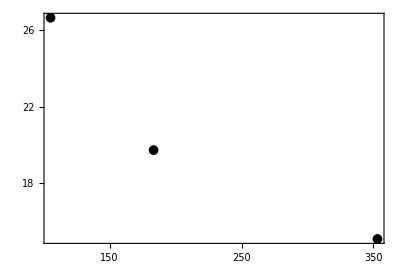

```mathematica
mtcars//
	GroupBy[#cyl&]//
	Map[summarize[{"avg_mpg"->Function[Mean@#mpg],"avg_disp"->Function[Mean@#disp]}]]//
	Values//
	ggplot[geomPoint["y"->"avg_mpg","x"->"avg_disp"]]
```

```mathematica
(*Takes a long time*)
(*diamonds//
	ggplot[geomPoint["x"->"carat","y"->"price","alpha"->Opacity[0.02]]]*)
```

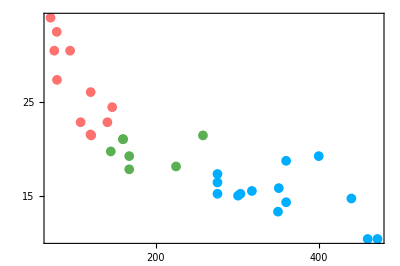

```mathematica
mtcars//
	MapAt[ToString,{{All,"cyl"},{All,"gear"}}]//
	ggplot[geomPoint["x"->"disp","y"->"mpg","color"->"cyl"]]
```

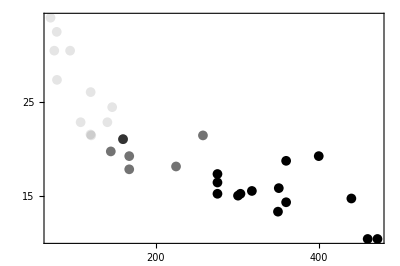

```mathematica
mtcars//
	ggplot[geomPoint["x"->"disp","y"->"mpg","alpha"->"cyl"]]
```

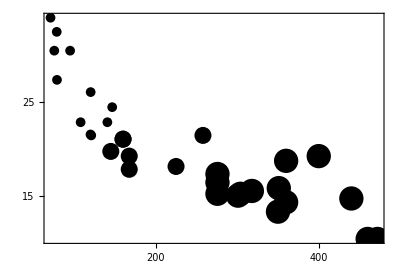

```mathematica
mtcars//
	ggplot[geomPoint["x"->"disp","y"->"mpg","size"->"cyl"]]
```

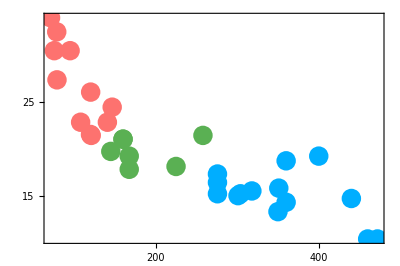

```mathematica
mtcars//
	MapAt[ToString,{All,"cyl"}]//
	ggplot[geomPoint["x"->"disp","y"->"mpg","color"->"cyl","size"->20]]
```

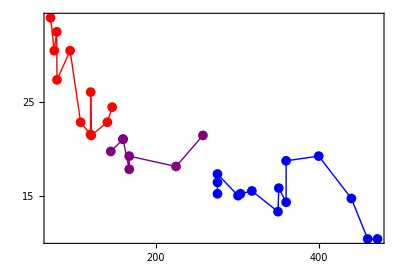

```mathematica
mtcars//
	ggplot[{
		geomPoint["x"->"disp","y"->"mpg","color"->"cyl"],
		geomLine["x"->"disp","y"->"mpg","color"->"cyl"]
	}]
```

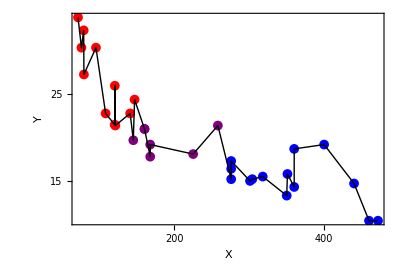

```mathematica
mtcars//
	ggplot[{
		geomPoint["x"->"disp","y"->"mpg","color"->"cyl"],
		geomLine["x"->"disp","y"->"mpg","color"->Black]
	},FrameLabel->{"X","Y"}]
```

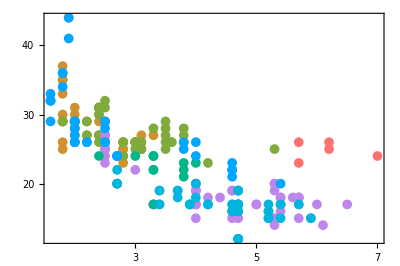

```mathematica
mpg//
	ggplot[geomPoint["x"->"displ","y"->"hwy","color"->"class"]]
```

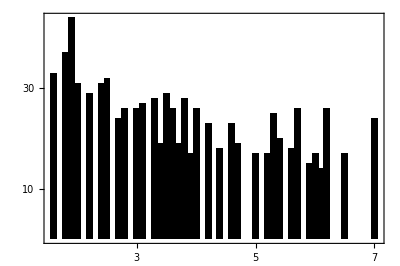

```mathematica
mpg//
	ggplot[geomCol["x"->"displ","y"->"hwy"]]
```